```mathematica
ClearAll["Global`*"]
```

```mathematica
(* for all (r,s) with height below fixed x, how many give newly reducible third iterates? *)
```

```mathematica
gammaplus[m_,d_,y_]:=y(-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
gammaminus[m_,d_,y_]:=-y(-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;

(* given rational (r,s=d) in A^2, returns (m,y) that is a solution to S *)
ϕ[r_,s_]:={(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r),(-4+r^2-4 s^2+s^4)/(2 r)};

(* returns the number and %age of (r,s) with height ≤n that give newly reducible third iterates *)
NRTIsHeightLePlus[n_]:=Module[{r,s,m,y,γ,f,totalnum,NRTInum},
totalnum=0;
NRTInum=0;
Do[Do[Do[Do[
If[GCD[r1,r2]==1&&GCD[s1,s2]==1&&r1≠0,
totalnum++;
r=r1/r2;
s=s1/s2;
{m,y}=ϕ[r,s];
γ=gammaplus[m,s,y];
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[f[x]]],
NRTInum++;
]
]
,{r1,-n,n}],{r2,1,n}],{s1,-n,n}],{s2,1,n}];
Return[{ToString[NRTInum]<>"/"<>ToString[totalnum],N[NRTInum/totalnum]}];
];
```

```mathematica
(* note  # rationals w height leq k is at most 2 k^2+k http://www.math.leidenuniv.nl/~streng/elliptic/homework5.pdf  *)
```

```mathematica
(*  SubPlus[γ]  *)
```

```mathematica
(* e.g. H=1, we have 6 possibilities, 2/6 give newly reducible 3rd iterate *)
Do[
{r,s}=rs;
{m,y}=ϕ[r,s];
γ=gammaplus[m,s,y];
f[x_]:=(x-γ)^2+γ+m;
Print[IrreduciblePolynomialQ[f[f[x]]]];
,{rs,{{1/1,0/1},{-1/1,0/1},{1/1,1/1},{-1/1,1/1},{1/1,-1/1},{-1/1,-1/1}}}]
```

False

False

True

False

True

False

```mathematica
NRTIsHeightLePlus[1]
```

{2/6,0.333333}

```mathematica
numNRTIs=NRTIsHeightLePlus/@Range[9];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLePlus[10]];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLePlus[11]];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLePlus[12]];
```

```mathematica
numNRTIs//MatrixForm
```

(2/6 | 0.333333
28/42 | 0.666667
182/210 | 0.866667
464/506 | 0.916996
1400/1482 | 0.944669
2064/2162 | 0.954672
4834/4970 | 0.972636
7298/7482 | 0.975408
11932/12210 | 0.977232
15666/16002 | 0.979003
27310/27722 | 0.985138
32864/33306 | 0.986729)

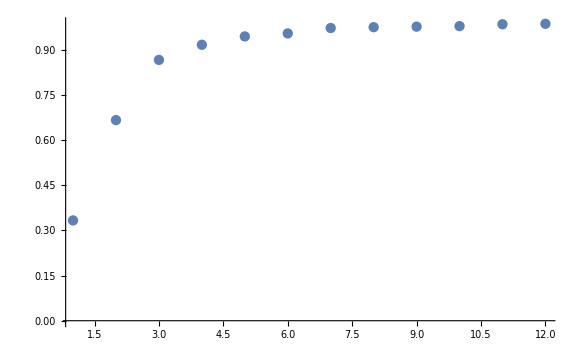

```mathematica
ListPlot[numNRTIs[[All,2]],PlotRange->All]
```

```mathematica
data=Transpose[{Range[12],numNRTIs[[All,2]]}];
```

```mathematica
logg=Fit[data,{1,Log[x],Log[x]^2},x]
```

0.333387+0.60979 Log[x]-0.142249 Log[x]^2

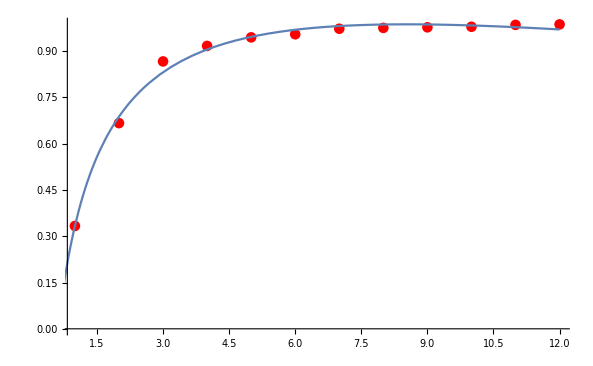

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotRange->All],Plot[{logg},{x,0,12},PlotRange->All]]
```

```mathematica
{m,y}=ϕ[r1/r2,s1/s2];
γ=gammaplus[m,s1/s2,y];
-m-γ//Simplify
m^2+m+γ//Simplify
```

(s1^2 (-r2 s1^2+2 r1 s2^2+4 r2 s2^2) (-2 r1 r2 s1^2 s2^2+r1^2 s2^4+r2^2 (s1^4-4 s1^2 s2^2-4 s2^4))^2)/(256 r1^2 r2^3 s2^12)

1/(256 r1^2 r2^3 s2^12)(-r2 s1^2+r1 s2^2+2 r2 s2^2)^2 (-2 r1^3 s1^2 s2^6+r2^3 (s1^4-4 s1^2 s2^2-4 s2^4)^2+r1^2 r2 s2^4 (5 s1^4+4 s1^2 s2^2+4 s2^4)+4 r1 r2^2 s2^2 (-s1^6+3 s1^4 s2^2+8 s1^2 s2^4+4 s2^6))

```mathematica
(*these must be non-square*)
(-r2 s1^2+2 r1 s2^2+4 r2 s2^2)r2//Expand
(-2 r1^3 s1^2 s2^6+r2^3 (s1^4-4 s1^2 s2^2-4 s2^4)^2+r1^2 r2 s2^4 (5 s1^4+4 s1^2 s2^2+4 s2^4)+4 r1 r2^2 s2^2 (-s1^6+3 s1^4 s2^2+8 s1^2 s2^4+4 s2^6))r2//Expand
```

-r2^2 s1^2+2 r1 r2 s2^2+4 r2^2 s2^2

r2^4 s1^8-4 r1 r2^3 s1^6 s2^2-8 r2^4 s1^6 s2^2+5 r1^2 r2^2 s1^4 s2^4+12 r1 r2^3 s1^4 s2^4+8 r2^4 s1^4 s2^4-2 r1^3 r2 s1^2 s2^6+4 r1^2 r2^2 s1^2 s2^6+32 r1 r2^3 s1^2 s2^6+32 r2^4 s1^2 s2^6+4 r1^2 r2^2 s2^8+16 r1 r2^3 s2^8+16 r2^4 s2^8

```mathematica
(*  SubMinus[γ]  *)
```

```mathematica
NRTIsHeightLeMinus[n_]:=Module[{r,s,m,y,γ,f,totalnum,NRTInum},
totalnum=0;
NRTInum=0;
Do[Do[Do[Do[
If[GCD[r1,r2]==1&&GCD[s1,s2]==1&&r1≠0,
totalnum++;
r=r1/r2;
s=s1/s2;
{m,y}=ϕ[r,s];
γ=gammaminus[m,s,y];
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[f[x]]],
NRTInum++;
]
]
,{r1,-n,n}],{r2,1,n}],{s1,-n,n}],{s2,1,n}];
Return[{ToString[NRTInum]<>"/"<>ToString[totalnum],N[NRTInum/totalnum]}];
];
```

```mathematica
(* e.g. H=1, we have 6 possibilities, 4/6 give newly reducible 3rd iterate *)
Do[
{r,s}=rs;
{m,y}=ϕ[r,s];
γ=gammaminus[m,s,y];
f[x_]:=(x-γ)^2+γ+m;
Print[IrreduciblePolynomialQ[f[f[x]]]];
,{rs,{{1/1,0/1},{-1/1,0/1},{1/1,1/1},{-1/1,1/1},{1/1,-1/1},{-1/1,-1/1}}}]
```

False

False

True

True

True

«1 more identical outputs»

```mathematica
NRTIsHeightLeMinus[1]
```

{4/6,0.666667}

```mathematica
numNRTIsMinus=NRTIsHeightLeMinus/@Range[9];
```

```mathematica
AppendTo[numNRTIsMinus,NRTIsHeightLeMinus[10]];
```

```mathematica
AppendTo[numNRTIsMinus,NRTIsHeightLeMinus[11]];
```

```mathematica
AppendTo[numNRTIsMinus,NRTIsHeightLeMinus[12]];
```

```mathematica
GraphicsRow[{numNRTIsMinus//MatrixForm,numNRTIs//MatrixForm}]
```

-Graphics-

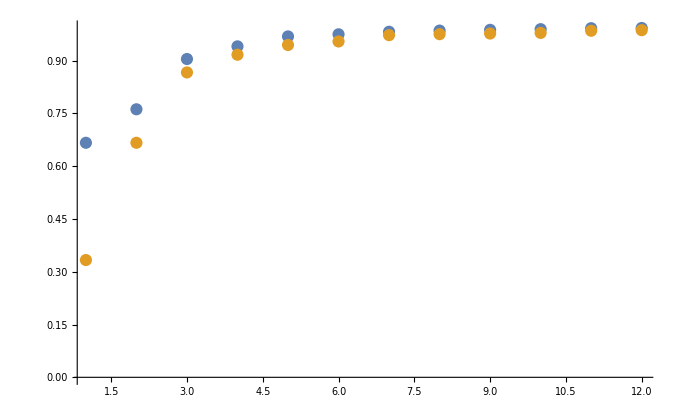

```mathematica
ListPlot[{numNRTIsMinus[[All,2]],numNRTIs[[All,2]]},PlotRange->All]
```